```mathematica
ClearAll
```

ClearAll

```mathematica
1+1
```

2

```mathematica
n0=-4;
nf=2;
```

```mathematica
ζ[n_]=(1+ⅈ*-Exp[-n])*Exp[-ⅈ*-Exp[-n]];
cζ[n_]:=(1-ⅈ*-Exp[-n])*Exp[ⅈ*-Exp[-n]];
η[n_]:=1
```

```mathematica
s=NDSolve[{x1'[n]==-ⅈ*η[n]/(-Exp[-n]^3)*(D[cζ[n],n]*ζ[n]*y1[n]+D[cζ[n],n]*cζ[n]*y2[n]), x2'[n]==-ⅈ*η[n]/(-Exp[-n]^3)*(-D[ζ[n],n]*ζ[n]*y1[n]+-D[ζ[n],n]*cζ[n]*y2[n]),y1'[n]==ⅈ*η[n]/(-Exp[-n]^3)*(-D[ζ[n],n]*cζ[n]*x1[n]+-D[cζ[n],n]*cζ[n]*x2[n]),y2'[n]==-ⅈ*η[n]/(-Exp[-n]^3)*(D[ζ[n],n]*ζ[n]*x1[n]+D[cζ[n],n]*ζ[n]*x2[n]), x1[n0]==1, x2[n0]==0, y1[n0]==0, y2[n0]==0},{x1,x2,y1,y2},{n,n0,nf}]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…],y1→InterpolatingFunction[…],y2→InterpolatingFunction[…]}}

```mathematica
xx1[n_]:=x1[n]/.s
xx2[n_]:=x2[n]/.s
yy1[n_]:=y1[n]/.s
yy2[n_]:=y2[n]/.s
```

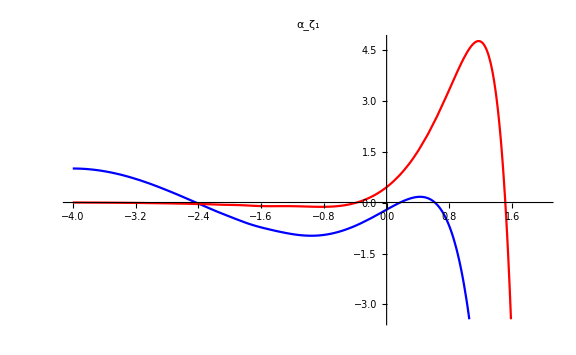

```mathematica
p1=ReImPlot[xx1[n], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing[None], Red]}, PlotLabel->Subscript[α, Subscript[ζ, 1]], ImageSize->Large]
```

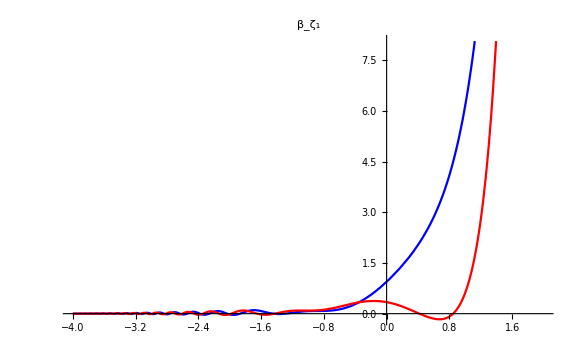

```mathematica
p2=ReImPlot[xx2[n], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing[None], Red]}, PlotLabel->Subscript[β, Subscript[ζ, 1]], ImageSize->Large]
```

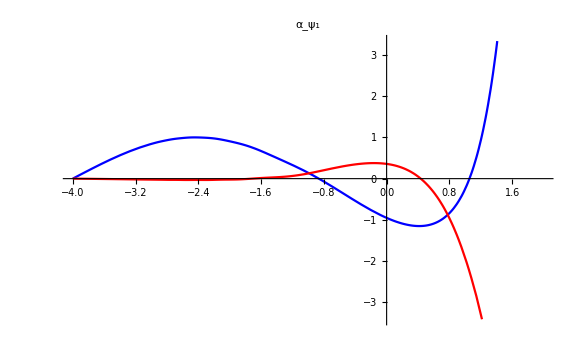

```mathematica
p3=ReImPlot[yy1[n], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing[None], Red]}, PlotLabel->Subscript[α, Subscript[ψ, 1]], ImageSize->Large]
```

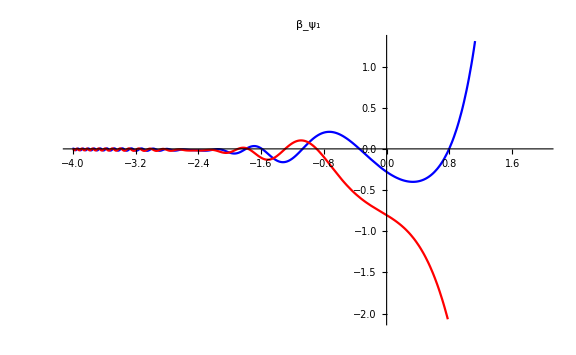

```mathematica
p4=ReImPlot[yy2[n], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing[None], Red]}, PlotLabel->Subscript[β, Subscript[ψ, 1]],ImageSize->Large]
```

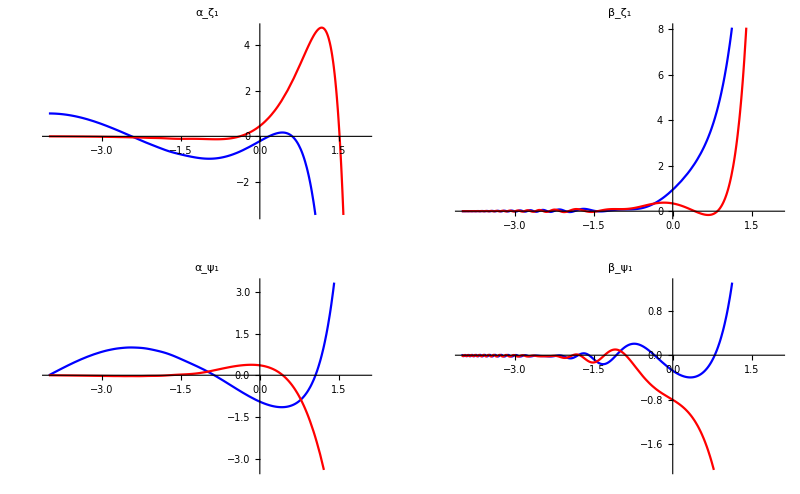

```mathematica
GraphicsGrid[{{p1,p2},{p3,p4}}, ImageSize->Full]
```